```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Documents/GitHub/LiRA/code/nb

## Eigenvalues

### Import data

```mathematica
tabEigVals=Import["../data/Dump_Eigenvalues.hf5",{"Datasets","tabEigVals"}];
tabEigValsPhys=Import["../data/Dump_Eigenvalues.hf5",{"Datasets","tabEigValsPhys"}];
tabEigValsReal=tabEigVals[[All,1]];
tabEigValsImag=tabEigVals[[All,2]];
tabEigValsPhysReal=tabEigValsPhys[[All,1]];
tabEigValsPhysImag=tabEigValsPhys[[All,2]];
tabEigValsPlane={tabEigValsReal,tabEigValsImag}//Transpose;
tabEigValsPhysPlane={tabEigValsPhysReal,tabEigValsPhysImag}//Transpose;
```

### Plot Nyquist diagramm

2

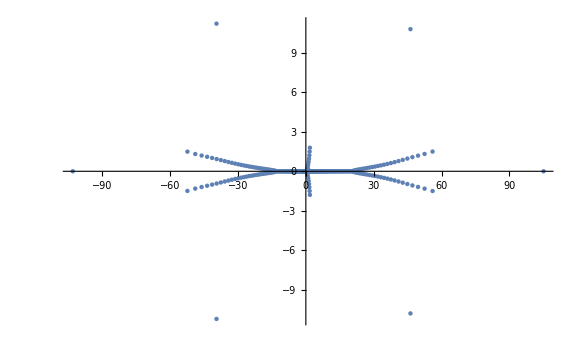

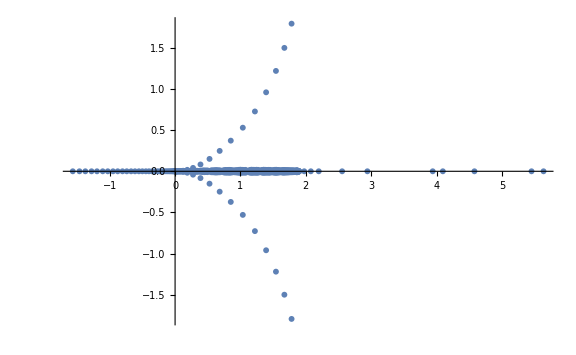

```mathematica
imMax=2
pEig=ListPlot[{tabEigValsPlane},ImageSize->Large,PlotRange->All]
pEigPhys=ListPlot[{tabEigValsPhysPlane},ImageSize->Large,PlotRange->All]
```

### Save data

```mathematica
Export["../graphs/growthRateMathematica.png",pGR]
```